# Higgs to digluon SM - attempt 1 with the FeynArts pipeline

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

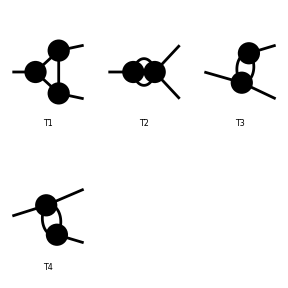

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/SMQCD.mod

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 ad/becf/dedfef.m, 2 diagrams

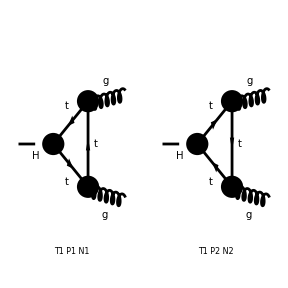

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[5],V[5]},InsertionLevel->{Particles},Model->"SMQCD",
(*,ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[13,{2,3}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]}*)Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[(*OffShell[*)CreateFeynAmp[diag1](*,2-> mg1,3-> mg2]*),FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp((S(1) | k(1) | MH | {})→(V(5,{Glu2}) | k(2) | 0 | {√3 ColorCharge}
V(5,{Glu3}) | k(3) | 0 | {√3 ColorCharge}))(1/(π MW SW)Alfas EL MT2 Mat(SUN1) (-1/2 Abb1 C0i(cc0,0,0,MH2,MT2,MT2,MT2)-Abb2 C0i(cc2,0,0,MH2,MT2,MT2,MT2)+Pair1 (B0i(bb0,0,MT2,MT2)-4 C0i(cc00,0,0,MH2,MT2,MT2,MT2))-4 Pair2 Pair3 (C0i(cc12,0,0,MH2,MT2,MT2,MT2)+C0i(cc22,0,0,MH2,MT2,MT2,MT2))))

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp((S(1) | k(1) | MH | {})→(V(5,{Glu2}) | k(2) | 0 | {√3 ColorCharge}
V(5,{Glu3}) | k(3) | 0 | {√3 ColorCharge}))(0)

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

mat= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-5.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
(*mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify*)
```

# Input point

## Inputs

```mathematica
stopM1 = 250;
stopM2 = 10000;
mixT = 0;
muM = 250;
betaA = 1.47; (*tan beta = 10*)
alphaA = betaA - (Pi/2);
offM1 =0.0001;
offM2 = 0.0001;
Clear[matSq,c1,c2,ghSS,h11,h12,h22,z11,z12,z22,m,mh,mZ,mW]
```

# FeynArts Evaluation

## Numerical Evaluation

```mathematica
matPostSub = mat//.Subexpr[]//. mg1 -> offM1 //.mg2-> offM2
```

1/(π MW2 SW2)4 Alfa Alfas2 MT2^2 (4 Conjugate[C0i(cc2,0,0,MH2,MT2,MT2,MT2)] (MH2^2 (C0i(cc0,0,0,MH2,MT2,MT2,MT2)+6 (C0i(cc12,0,0,MH2,MT2,MT2,MT2)+C0i(cc22,0,0,MH2,MT2,MT2,MT2))+5 C0i(cc2,0,0,MH2,MT2,MT2,MT2))-MH2 (B0i(bb0,0,MT2,MT2)-4 C0i(cc00,0,0,MH2,MT2,MT2,MT2)))+4 (Conjugate[C0i(cc12,0,0,MH2,MT2,MT2,MT2)]+Conjugate[C0i(cc22,0,0,MH2,MT2,MT2,MT2)]) (-2 MH2 B0i(bb0,0,MT2,MT2)+MH2^2 (C0i(cc0,0,0,MH2,MT2,MT2,MT2)+6 C0i(cc2,0,0,MH2,MT2,MT2,MT2)+8 C0i(cc22,0,0,MH2,MT2,MT2,MT2))+8 (MH2 C0i(cc00,0,0,MH2,MT2,MT2,MT2)+MH2^2 C0i(cc12,0,0,MH2,MT2,MT2,MT2)))-4 Conjugate[B0i(bb0,0,MT2,MT2)] (-B0i(bb0,0,MT2,MT2)+4 C0i(cc00,0,0,MH2,MT2,MT2,MT2)+MH2 (2 (C0i(cc12,0,0,MH2,MT2,MT2,MT2)+C0i(cc22,0,0,MH2,MT2,MT2,MT2))+C0i(cc2,0,0,MH2,MT2,MT2,MT2)))+16 Conjugate[C0i(cc00,0,0,MH2,MT2,MT2,MT2)] (-B0i(bb0,0,MT2,MT2)+4 C0i(cc00,0,0,MH2,MT2,MT2,MT2)+MH2 (2 (C0i(cc12,0,0,MH2,MT2,MT2,MT2)+C0i(cc22,0,0,MH2,MT2,MT2,MT2))+C0i(cc2,0,0,MH2,MT2,MT2,MT2)))+MH2^2 Conjugate[C0i(cc0,0,0,MH2,MT2,MT2,MT2)] (C0i(cc0,0,0,MH2,MT2,MT2,MT2)+4 (C0i(cc12,0,0,MH2,MT2,MT2,MT2)+C0i(cc2,0,0,MH2,MT2,MT2,MT2)+C0i(cc22,0,0,MH2,MT2,MT2,MT2))))

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[higgs_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
MH-> 125,MH2->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
Alfas->0.12,Alfas2->(0.12)^2,
SW2->0.2228,CW-> (MW/MZ),CW2->(MW/MZ)^2}
MyMatrixElement[higgs_]:=matPostSub//.VALUES[higgs]//Simplify
```

```mathematica
feynArtsResult =Chop[MyMatrixElement[125]]
```

2.87447

Partial decay width:

```mathematica
MyDecayRate[higgs_]:=1/(32π higgs)MyMatrixElement[higgs]
```

```mathematica
digluonSMResults = MyDecayRate[125]
```

0.000228743